# Two-plant species eco-evolutionary model

```mathematica
Clear["Global`*"]
```

### Ecological dynamics (Eqs. 9)

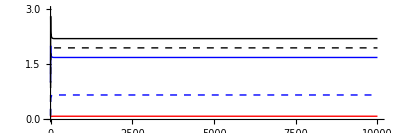

```mathematica
(* Coevolved ecological parameters (Supplementary Tables 1,2) *)
param={H->0.1,ϵ->1,mW->0.005,mD->0.003,dW->0.25,dD->0.3,dA->0.2};
end=10000; (* how long to run ecological model *)

(* Population dynamics *)
dDwt=Dw'[t]==Dw[t]((1-Dw[t])+((bW vW A[t])/(H+vW A[t]))-hW Lw[t]);
dDdt=Dd'[t]==Dd[t]((1-Dd[t])+((bD vD A[t])/(H+vD A[t]))-hD Ld[t]);
dLwt=Lw'[t]==ϵ eW vW Dw[t] A[t]-mW hW Lw[t]-dW Lw[t];
dLdt=Ld'[t]==ϵ eD vD Dd[t] A[t]-mD hD Ld[t]-dD Ld[t];
dAt=A'[t]==mW hW Lw[t]+mD hD Ld[t]-dA A[t];
ecoEqsol=ParametricNDSolve[{dDwt/.param,dDdt/.param,dLwt/.param,dLdt/.param,dAt/.param,Dw[0]==1,Dd[0]==1,Lw[0]==0.1,Ld[0]==0.1,A[0]==0.1},{Dw,Dd,Lw,Ld,A},{t,0,end},{bW,vW,hW,bD,vD,hD,eW,eD}];

(* Plot ecological dynamics *)
Plot[{Dw[4.7,4.3,1.3,3.5,2.3,2.5,0.6,0.6][t]/.ecoEqsol,Dd[4.7,4.3,1.3,3.5,2.3,2.5,0.6,0.6][t]/.ecoEqsol,Lw[4.7,4.3,1.3,3.5,2.3,2.5,0.6,0.6][t]/.ecoEqsol,Ld[4.7,4.3,1.3,3.5,2.3,2.5,0.6,0.6][t]/.ecoEqsol,A[4.7,4.3,1.3,3.5,2.3,2.5,0.6,0.6][t]/.ecoEqsol},{t,0,end},PlotRange->{{0,end},{0,3}},AspectRatio->1/3,PlotStyle->{{Black,Thick},{Blue,Thick},{Black,Dashed,Thick},{Blue,Dashed,Thick},{Red,Thick}},TicksStyle->Black,AxesStyle->Black,LabelStyle->Directive[FontSize->12]]
```

### Coevolutionary dynamics

#### Invasion fitness and selection gradients

```mathematica
(* Note: vPw, vPd, etc. used instead of x^P_i as in manuscript *)
(* Note: vSi, hSi, bSi used instead of V_i', H_i', R_i' as in manuscript *)
(* Note: cIVi, cIHi used instead of c^V_I,i and c^H_I,i as in manuscript *)
(* Note: e used instead of ϵ as in manuscript *)

(* Resident trait functions *)
vWf=vWmax/(1+Exp[-vSw(vPw+vIw)]);vDf=vDmax/(1+Exp[-vSd(vPd+vId)]);
hWf=hWmax/(1+Exp[hSw(hPw-hIw)]);hDf=hDmax/(1+Exp[hSd(hPd-hId)]);
bWf=bWmax(2/(1+Exp[-bSw bPw])-1);bDf=bDmax(2/(1+Exp[-bSd bPd])-1);
eWf=Exp[-(cIHw hIw^2+cIVw vIw^2)];eDf=Exp[-(cIHd hId^2+cIVd vId^2)];

(* Mutant insect trait functions *)
vWfMut=vWmax/(1+Exp[-vSw(vPw+vIwMut)]);vDfMut=vDmax/(1+Exp[-vSd(vPd+vIdMut)]);
hWfMut=hWmax/(1+Exp[hSw(hPw-hIwMut)]);hDfMut=hDmax/(1+Exp[hSd(hPd-hIdMut)]);
eWfMut=Exp[-(cIHw hIwMut^2+cIVw vIwMut^2)];eDfMut=Exp[-(cIHd hIdMut^2+cIVd vIdMut^2)];

(* Invasion fitness *)
(* D. wrightii *)
Ww=(1-(1+cBw (bPwMut-bPw)+cPVw (vPwMut-vPw)+cPHw(hPwMut-hPw))DwStar)+((bWmax(2/(1+Exp[-bSw bPwMut])-1)(vWmax/(1+Exp[-vSw(vPwMut+vIw)])) Astar)/(H+(vWmax/(1+Exp[-vSw(vPwMut+vIw)])) Astar))-(hWmax/(1+Exp[hSw(hPwMut-hIw)]))LwStar;
(* D. discolor *)
Wd=(1-(1+cBd (bPdMut-bPd)+cPVd (vPdMut-vPd)+cPHd(hPdMut-hPd))DdStar)+((bDmax(2/(1+Exp[-bSd bPdMut])-1)(vDmax/(1+Exp[-vSd(vPdMut+vId)])) Astar)/(H+(vDmax/(1+Exp[-vSd(vPdMut+vId)])) Astar))-(hDmax/(1+Exp[hSd(hPdMut-hId)]))LdStar;
(* M. sexta *)
Wi=Root[dA dD dW+dA dW hDfMut mD+dA dD hWfMut mW+dA hDfMut hWfMut mD mW-DdStar dW e eDfMut hDfMut mD vDfMut-DdStar e eDfMut hDfMut hWfMut mD mW vDfMut-dD DwStar e eWfMut hWfMut mW vWfMut-DwStar e eWfMut hDfMut hWfMut mD mW vWfMut+(dA dD+dA dW+dD dW+dA hDfMut mD+dW hDfMut mD+dA hWfMut mW+dD hWfMut mW+hDfMut hWfMut mD mW-DdStar e eDfMut hDfMut mD vDfMut-DwStar e eWfMut hWfMut mW vWfMut) #1+(dA+dD+dW+hDfMut mD+hWfMut mW) #1^2+#1^3&,3];

(* Selection Gradients *)
(* D. wrightii *)
dHWdt=D[Ww,hPwMut]/.hPwMut->hPw/.vPwMut->vPw/.bPwMut->bPw;
dVWdt=D[Ww,vPwMut]/.hPwMut->hPw/.vPwMut->vPw/.bPwMut->bPw;
dBWdt=D[Ww,bPwMut]/.hPwMut->hPw/.vPwMut->vPw/.bPwMut->bPw;
(* D. discolor *)
dHDdt=D[Wd,hPdMut]/.hPdMut->hPd/.vPdMut->vPd/.bPdMut->bPd;
dVDdt=D[Wd,vPdMut]/.hPdMut->hPd/.vPdMut->vPd/.bPdMut->bPd;
dBDdt=D[Wd,bPdMut]/.hPdMut->hPd/.vPdMut->vPd/.bPdMut->bPd;
(* M. sexta *)
dHiWdt=D[Wi,hIwMut]/.hIwMut->hIw/.vIwMut->vIw/.hIdMut->hId/.vIdMut->vId;
dViWdt=D[Wi,vIwMut]/.hIwMut->hIw/.vIwMut->vIw/.hIdMut->hId/.vIdMut->vId;
dHiDdt=D[Wi,hIdMut]/.hIwMut->hIw/.vIwMut->vIw/.hIdMut->hId/.vIdMut->vId;
dViDdt=D[Wi,vIdMut]/.hIwMut->hIw/.vIwMut->vIw/.hIdMut->hId/.vIdMut->vId;
```

#### Simulate evolutionary dynamics

##### Note: The error “NDSolve: The function value ... is not a real number when the arguments are ... ” indicates evolutionary purging of the insect. The error occurs because the insect equilibrium becomes an imaginary number when it is extinct. To avoid evolutionary purging, try varying the value of cPVi and/or cPHi or increasing vMax Note: If host evolves zero defense, try increasing hMax

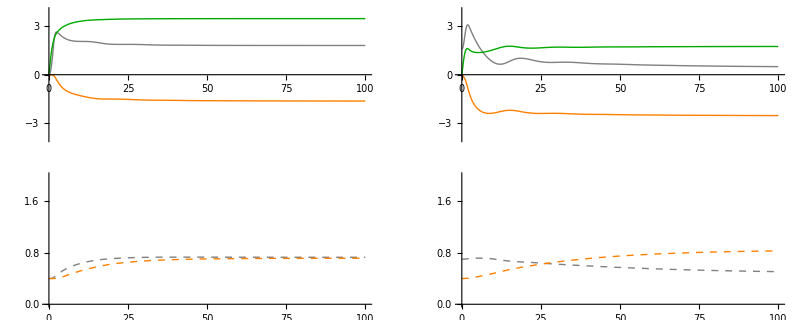

hPw: 1.81544 vPw: -1.63544 bPw: 3.48461

hPd: 0.501724 vPd: -2.53891 bPd: 1.75395

hIw: 0.729339 vIw: 0.714715 hId: 0.506412 vId: 0.828908

Wrightii_v→4.27215 Wrightii_h→1.26177 Wrightii_b→4.70247

Discolor_v→2.29744 Discolor_h→2.50586 Discolor_b→3.5245

Wrightii_e→0.593703 Discolor_e→0.623896

Wrightii density:2.26741 Discolor density:1.66789

```mathematica
(* PARAMETERS *)
(* D. wrightii and D. discolor *)
(* Note: cBi, cPVi, cPHi used instead of c^B_P,i, c^V_P,i, c^H_P,i as in manuscript *)
(* Note: For ancestral interaction, set bWmax = 0, bDmax = 0, cBw = 0, cBd = 0, cPVw = 0, and cPVd = 0 *)
(* Both Datura species *)
evoParam={vWmax->15,vDmax->15,hWmax->5,hDmax->5,bWmax->5,bDmax->5,H->0.1,e->1,mW->0.005,mD->0.003,dW->0.25,dD->0.3,dA->0.2,vSw->1,vSd->1,hSw->1,hSd->1,bSw->1,bSd->1,cBw->0.1,cBd->0.5,cPVw->0.25,cPVd->0.4,cPHw->0.8,cPHd->0.5,cIVw->0.5,cIVd->0.5,cIHw->0.5,cIHd->0.5,hPwInit->0,vPwInit->0,bPwInit->0,hPdInit->1.6,vPdInit->0,bPdInit->0,hIwInit->0.4,vIwInit->0.4,hIdInit->0.7,vIdInit->0.4};

(* D. wrightii with P. parviflora *)
(* Note: using D. discolor parameters for P. parviflora *)
(* Note: bDmax = 0 and cPVd = 0 because for P. parviflora, floral visitation is not possible *)
(* Note: For ancestral interaction, set bWmax = 0, bDmax = 0, cBw = 0, cBd = 0, cPVw = 0, and cPVd = 0 *)
(*evoParam={vWmax->15,vDmax->15,hWmax->5,hDmax->5,bWmax->5,bDmax->0,H->0.1,e->1,mW->0.005,mD->0.01,dW->0.25,dD->0.25,dA->0.2,vSw->1,vSd->1,hSw->1,hSd->1,bSw->1,bSd->1,cBw->0.1,cBd->0,cPVw->0.25,cPVd->0.,cPHw->0.8,cPHd->0.5,cIVw->0.5,cIVd->0.5,cIHw->0.5,cIHd->0.5,hPwInit->1.7,vPwInit->0,bPwInit->0,hPdInit->2.5,vPdInit->0,bPdInit->0,hIwInit->0.7,vIwInit->0.4,hIdInit->0.8,vIdInit->0.4};*)

(* D. discolor with P. parviflora *)
(* Note: using D. wrightii parameters for P. parviflora *)
(* Note: bWmax = 0 and cPVw = 0 because for P. parviflora, floral visitation is not possible *)
(* Note: For ancestral interaction, set bWmax = 0, bDmax = 0, cBw = 0, cBd = 0, cPVw = 0, and cPVd = 0 *)
(*evoParam={vWmax->15,vDmax->15,hWmax->5,hDmax->5,bWmax->0,bDmax->5,H->0.1,e->1,mW->0.01,mD->0.003,dW->0.25,dD->0.3,dA->0.2,vSw->1,vSd->1,hSw->1,hSd->1,bSw->1,bSd->1,cBw->0,cBd->0.5,cPVw->0,cPVd->0.4,cPHw->0.5,cPHd->0.5,cIVw->0.5,cIVd->0.5,cIHw->0.5,cIHd->0.5,hPwInit->2.1,vPwInit->0,bPwInit->0,hPdInit->1.8,vPdInit->0,bPdInit->0,hIwInit->0.8,vIwInit->0.4,hIdInit->0.7,vIdInit->0.4};*)
evoEnd=100; (* Evolutionary time-scale *)
end=1000; (* Ecological time-scale *)

(* Ecological dynamics (Eq. 10) *)
(* Note: vPw1, vPd1, etc. used to avoid errors when simulating eco-evolutionary dynamics *)
dDwt=Dw'[t]==Dw[t]((1-Dw[t])+((bWmax(2/(1+Exp[-bSw bPw1])-1)(vWmax/(1+Exp[-vSw(vPw1+vIw1)])) A[t])/(H+(vWmax/(1+Exp[-vSw(vPw1+vIw1)])) A[t]))-(hWmax/(1+Exp[hSw(hPw1-hIw1)])) Lw[t]);
dDdt=Dd'[t]==Dd[t]((1-Dd[t])+((bDmax(2/(1+Exp[-bSd bPd1])-1)(vDmax/(1+Exp[-vSd(vPd1+vId1)])) A[t])/(H+(vDmax/(1+Exp[-vSd(vPd1+vId1)])) A[t]))-(hDmax/(1+Exp[hSd(hPd1-hId1)])) Ld[t]);
dLwt=Lw'[t]==e Exp[-(cIHw hIw1^2+cIVw vIw1^2)] (vWmax/(1+Exp[-vSw(vPw1+vIw1)])) Dw[t] A[t]-mW (hWmax/(1+Exp[hSw(hPw1-hIw1)])) Lw[t]-dW Lw[t];
dLdt=Ld'[t]==e Exp[-(cIHd hId1^2+cIVd vId1^2)] (vDmax/(1+Exp[-vSd(vPd1+vId1)])) Dd[t] A[t]-mD (hDmax/(1+Exp[hSd(hPd1-hId1)])) Ld[t]-dD Ld[t];
dAt=A'[t]==mW (hWmax/(1+Exp[hSw(hPw1-hIw1)])) Lw[t]+mD (hDmax/(1+Exp[hSd(hPd1-hId1)])) Ld[t]-dA A[t];
eqsol=ParametricNDSolve[{dDwt/.evoParam,dDdt/.evoParam,dLwt/.evoParam,dLdt/.evoParam,dAt/.evoParam,Dw[0]==1,Dd[0]==1,Lw[0]==0.1,Ld[0]==0.1,A[0]==0.1},{Dw,Dd,Lw,Ld,A},{t,0,end}, {hPw1,vPw1,bPw1,hPd1,vPd1,bPd1,hIw1,vIw1,hId1,vId1},MaxSteps->Infinity,AccuracyGoal->Infinity];

(* Evolutionary dynamics *)
Off[NDSolve::nrnum1]
Off[NDSolve::evcvmit]
Off[InterpolatingFunction::dmval]
dHWt=hPw'[T]==-cPHw (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)+(ⅇ^((-hIw[T]+hPw[T]) hSw) hSw hWmax (Lw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol))/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))^2;
dVWt=vPw'[T]==-cPVw (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)-((A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)^2 ⅇ^(-(vIw[T]+vPw[T]) vSw) (-1+2/(1+ⅇ^(-bPw[T] bSw))) bWmax vSw vWmax^2)/((1+ⅇ^(-(vIw[T]+vPw[T]) vSw))^3 (H+1/(1+ⅇ^(-(vIw[T]+vPw[T]) vSw))(A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) vWmax)^2)+((A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) ⅇ^(-(vIw[T]+vPw[T]) vSw) (-1+2/(1+ⅇ^(-bPw[T] bSw))) bWmax vSw vWmax)/((1+ⅇ^(-(vIw[T]+vPw[T]) vSw))^2 (H+1/(1+ⅇ^(-(vIw[T]+vPw[T]) vSw))(A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) vWmax));
dBWt=bPw'[T]==-cBw (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)+(2 (A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) ⅇ^(-bPw[T] bSw) bSw bWmax vWmax)/((1+ⅇ^(-bPw[T] bSw))^2 (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)) (H+1/(1+ⅇ^(-(vIw[T]+vPw[T]) vSw))(A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) vWmax));
dHDt=hPd'[T]==-cPHd (Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)+(ⅇ^((-hId[T]+hPd[T]) hSd) hDmax hSd (Ld[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol))/(1+ⅇ^((-hId[T]+hPd[T]) hSd))^2;
dVDt=vPd'[T]==-cPVd (Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)-((A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)^2 ⅇ^(-(vId[T]+vPd[T]) vSd) (-1+2/(1+ⅇ^(-bPd[T] bSd))) bDmax vDmax^2 vSd)/((1+ⅇ^(-(vId[T]+vPd[T]) vSd))^3 (H+1/(1+ⅇ^(-(vId[T]+vPd[T]) vSd))(A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) vDmax)^2)+((A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) ⅇ^(-(vId[T]+vPd[T]) vSd) (-1+2/(1+ⅇ^(-bPd[T] bSd))) bDmax vDmax vSd)/((1+ⅇ^(-(vId[T]+vPd[T]) vSd))^2 (H+1/(1+ⅇ^(-(vId[T]+vPd[T]) vSd))(A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) vDmax));
dBDt=bPd'[T]==-cBd (Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)+(2 (A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) ⅇ^(-bPd[T] bSd) bDmax bSd vDmax)/((1+ⅇ^(-bPd[T] bSd))^2 (1+ⅇ^(-(vId[T]+vPd[T]) vSd)) (H+1/(1+ⅇ^(-(vId[T]+vPd[T]) vSd))(A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) vDmax));
dHIWt=hIw'[T]==(-(dA dD ⅇ^((-hIw[T]+hPw[T]) hSw) hSw hWmax mW)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw))^2)-(dA ⅇ^((-hIw[T]+hPw[T]) hSw) hDmax hSw hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw))^2)+((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2+(-hIw[T]+hPw[T]) hSw-cIVd vId[T]^2)  hDmax hSw hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw))^2 (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(2 cIHw dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hIw[T] hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2+(-hIw[T]+hPw[T]) hSw-cIVw vIw[T]^2)  hSw hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw))^2 (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-(2 cIHw (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hIw[T] hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2+(-hIw[T]+hPw[T]) hSw-cIVw vIw[T]^2)  hDmax hSw hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw))^2 (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((dA ⅇ^((-hIw[T]+hPw[T]) hSw) hSw hWmax mW)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw))^2)+(dD ⅇ^((-hIw[T]+hPw[T]) hSw) hSw hWmax mW)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw))^2)+(ⅇ^((-hIw[T]+hPw[T]) hSw) hDmax hSw hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw))^2)+(2 cIHw (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hIw[T] hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2+(-hIw[T]+hPw[T]) hSw-cIVw vIw[T]^2)  hSw hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw))^2 (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3]-1/((1+ⅇ^((-hIw[T]+hPw[T]) hSw))^2)ⅇ^((-hIw[T]+hPw[T]) hSw) hSw hWmax mW Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3]^2)/(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+2 (dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3]+3 Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3]^2);
dVIWt=vIw'[T]==(-((2 cIVw dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vIw[T] vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw))))-(2 cIVw (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vIw[T] vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2-(vIw[T]+vPw[T]) vSw)  hWmax mW vSw vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw))^2)+((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2-(vIw[T]+vPw[T]) vSw)  hDmax hWmax mD mW vSw vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw))^2)-((2 cIVw (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vIw[T] vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2-(vIw[T]+vPw[T]) vSw)  hWmax mW vSw vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw))^2)) Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3])/(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+2 (dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3]+3 Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3]^2);
dHIDt=hId'[T]==(-(dA dW ⅇ^((-hId[T]+hPd[T]) hSd) hDmax hSd mD)/((1+ⅇ^((-hId[T]+hPd[T]) hSd))^2)-(dA ⅇ^((-hId[T]+hPd[T]) hSd) hDmax hSd hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd))^2 (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-(2 cIHd (Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hId[T] mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))+((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2+(-hId[T]+hPd[T]) hSd-cIVd vId[T]^2)  hDmax hSd mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd))^2 (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(2 cIHd (Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hId[T] hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))+((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2+(-hId[T]+hPd[T]) hSd-cIVd vId[T]^2)  hDmax hSd hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd))^2 (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))+((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2+(-hId[T]+hPd[T]) hSd-cIVw vIw[T]^2)  hDmax hSd hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd))^2 (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((dA ⅇ^((-hId[T]+hPd[T]) hSd) hDmax hSd mD)/((1+ⅇ^((-hId[T]+hPd[T]) hSd))^2)+(dW ⅇ^((-hId[T]+hPd[T]) hSd) hDmax hSd mD)/((1+ⅇ^((-hId[T]+hPd[T]) hSd))^2)+(ⅇ^((-hId[T]+hPd[T]) hSd) hDmax hSd hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd))^2 (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))+(2 cIHd (Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hId[T] mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2+(-hId[T]+hPd[T]) hSd-cIVd vId[T]^2)  hDmax hSd mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd))^2 (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))) Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3]-1/((1+ⅇ^((-hId[T]+hPd[T]) hSd))^2)ⅇ^((-hId[T]+hPd[T]) hSd) hDmax hSd mD Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3]^2)/(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+2 (dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3]+3 Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3]^2);
dVIDt=vId'[T]==(-((2 cIVd (Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax vId[T])/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd))))-(2 cIVd (Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax vId[T])/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))+((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2-(vId[T]+vPd[T]) vSd)  hDmax mD vDmax vSd)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd))^2)+((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2-(vId[T]+vPd[T]) vSd)  hDmax hWmax mD mW vDmax vSd)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd))^2)-((2 cIVd (Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax vId[T])/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2-(vId[T]+vPd[T]) vSd)  hDmax mD vDmax vSd)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd))^2)) Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3])/(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+2 (dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3]+3 Root[dA dD dW+(dA dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dA hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) dW e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax hWmax mD mW vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-(dD (Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hDmax hWmax mD mW vWmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))+(dA dD+dA dW+dD dW+(dA hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dW hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(dA hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(dD hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))+(hDmax hWmax mD mW)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^((-hIw[T]+hPw[T]) hSw)))-((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHd hId[T]^2-cIVd vId[T]^2)  hDmax mD vDmax)/((1+ⅇ^((-hId[T]+hPd[T]) hSd)) (1+ⅇ^(-(vId[T]+vPd[T]) vSd)))-((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol) e ⅇ^(-cIHw hIw[T]^2-cIVw vIw[T]^2)  hWmax mW vWmax)/((1+ⅇ^((-hIw[T]+hPw[T]) hSw)) (1+ⅇ^(-(vIw[T]+vPw[T]) vSw)))) #1+(dA+dD+dW+(hDmax mD)/(1+ⅇ^((-hId[T]+hPd[T]) hSd))+(hWmax mW)/(1+ⅇ^((-hIw[T]+hPw[T]) hSw))) #1^2+#1^3&,3]^2);

eqsolEvo=NDSolve[{dHWt/.evoParam,dVWt/.evoParam,dBWt/.evoParam,dHDt/.evoParam,dVDt/.evoParam,dBDt/.evoParam,dHIWt/.evoParam,dVIWt/.evoParam,dHIDt/.evoParam,dVIDt/.evoParam,hPw[0]==hPwInit/.evoParam,vPw[0]==vPwInit/.evoParam,bPw[0]==bPwInit/.evoParam,hPd[0]==hPdInit/.evoParam,vPd[0]==vPdInit/.evoParam,bPd[0]==bPdInit/.evoParam,hIw[0]==hIwInit/.evoParam,vIw[0]==vIwInit/.evoParam,hId[0]==hIdInit/.evoParam,vId[0]==vIdInit/.evoParam,WhenEvent[hPw[T]<-0.0001,hPw[T]->0],WhenEvent[hPd[T]<-0.0001,hPd[T]->0],WhenEvent[Im[vPw[T]]≠0,{"StopIntegration",end=T,Print["D. wrightii purges insect"]}],WhenEvent[Im[vPd[T]]≠0,{"StopIntegration",end=T,Print["D. discolor purges insect"]}]},{hPw,vPw,bPw,hPd,vPd,bPd,hIw,vIw,hId,vId},{T,0,evoEnd}];

(* Trait dynamics *)
GraphicsGrid[{{Plot[{hPw[t]/.eqsolEvo,vPw[t]/.eqsolEvo,bPw[t]/.eqsolEvo},{t,0,evoEnd},PlotRange->{{0,evoEnd},{-4,4}},PlotStyle->{{Gray,Thick},{Orange,Thick},{Darker[Green],Thick}},AspectRatio->0.4,TicksStyle->Black,AxesStyle->Black,LabelStyle->Directive[FontSize->12]],
Plot[{hPd[t]/.eqsolEvo,vPd[t]/.eqsolEvo,bPd[t]/.eqsolEvo},{t,0,evoEnd},PlotRange->{{0,evoEnd},{-4,4}},PlotStyle->{{Gray,Thick},{Orange,Thick},{Darker[Green],Thick}},AspectRatio->0.4,TicksStyle->Black,AxesStyle->Black,LabelStyle->Directive[FontSize->12]]},{Plot[{hIw[t]/.eqsolEvo,vIw[t]/.eqsolEvo},{t,0,evoEnd},PlotRange->{{0,evoEnd},{0,2}},PlotStyle->{{Gray,Dashed,Thick},{Orange,Dashed,Thick}},AspectRatio->0.4,TicksStyle->Black,AxesStyle->Black,LabelStyle->Directive[FontSize->12]],Plot[{hId[t]/.eqsolEvo,vId[t]/.eqsolEvo},{t,0,evoEnd},PlotRange->{{0,evoEnd},{0,2}},PlotStyle->{{Gray,Dashed,Thick},{Orange,Dashed,Thick}},AspectRatio->0.4,TicksStyle->Black,AxesStyle->Black,LabelStyle->Directive[FontSize->12]]}}]

(* Print trait values *)
Print["hPw: ",(hPw[evoEnd]/.eqsolEvo)[[1]]," vPw: ",(vPw[evoEnd]/.eqsolEvo)[[1]]," bPw: ",(bPw[evoEnd]/.eqsolEvo)[[1]]]
Print["hPd: ",(hPd[evoEnd]/.eqsolEvo)[[1]]," vPd: ",(vPd[evoEnd]/.eqsolEvo)[[1]]," bPd: ",(bPd[evoEnd]/.eqsolEvo)[[1]]]
Print["hIw: ",(hIw[evoEnd]/.eqsolEvo)[[1]]," vIw: ",(vIw[evoEnd]/.eqsolEvo)[[1]]," hId: ",(hId[evoEnd]/.eqsolEvo)[[1]]," vId: ",(vId[evoEnd]/.eqsolEvo)[[1]]]

(* Print trait functions *)
Print["Wrightii_v→",(vWmax/(1+Exp[-vSw((vPw[evoEnd]/.eqsolEvo)+(vIw[evoEnd]/.eqsolEvo))])/.evoParam)[[1]]," Wrightii_h→",(hWmax/(1+Exp[hSw ((hPw[evoEnd]/.eqsolEvo)-(hIw[evoEnd]/.eqsolEvo))])/.evoParam)[[1]]," Wrightii_b→",(bWmax(2/(1+Exp[-bSw (bPw[evoEnd]/.eqsolEvo)])-1)/.evoParam)[[1]]]
Print["Discolor_v→",(vDmax/(1+Exp[-vSd((vPd[evoEnd]/.eqsolEvo)+(vId[evoEnd]/.eqsolEvo))])/.evoParam)[[1]],
" Discolor_h→",(hDmax/(1+Exp[hSd((hPd[evoEnd]/.eqsolEvo)-(hId[evoEnd]/.eqsolEvo))])/.evoParam)[[1]],
" Discolor_b→",(bDmax(2/(1+Exp[-bSd (bPd[evoEnd]/.eqsolEvo)])-1)/.evoParam)[[1]]]
Print["Wrightii_e→",(Exp[-(cIHw (hIw[evoEnd]/.eqsolEvo)^2+cIVw (vIw[evoEnd]/.eqsolEvo)^2)]/.evoParam)[[1]],
" Discolor_e→",(Exp[-(cIHd (hId[evoEnd]/.eqsolEvo)^2+cIVd (vId[evoEnd]/.eqsolEvo)^2)]/.evoParam)[[1]]]
Print["Wrightii density:",((Dw[hPw[evoEnd],vPw[evoEnd],bPw[evoEnd],hPd[evoEnd],vPd[evoEnd],bPd[evoEnd],hIw[evoEnd],vIw[evoEnd],hId[evoEnd],vId[evoEnd]][end]/.eqsol)/.eqsolEvo)[[1]],
" Discolor density:",((Dd[hPw[evoEnd],vPw[evoEnd],bPw[evoEnd],hPd[evoEnd],vPd[evoEnd],bPd[evoEnd],hIw[evoEnd],vIw[evoEnd],hId[evoEnd],vId[evoEnd]][end]/.eqsol)/.eqsolEvo)[[1]]]
```

#### D. wrightii: Figure 3a

#### Parameter Space

NOTE: To simply create Figure 3a, please see section “Figure 3a” below.

```mathematica
(* Parameters: *)
param={hMax->5,H->0.1,ϵ->1,mW->0.005,mD->0.003,dW->0.25,dD->0.3,dA->0.2};

(* Population dynamics *)
dDwt=Dw'[t]==Dw[t]((1-Dw[t])+((bW vW A[t])/(H+vW A[t]))-hW Lw[t]);
dDdt=Dd'[t]==Dd[t]((1-Dd[t])+((bD vD A[t])/(H+vD A[t]))-hD Ld[t]);
dLwt=Lw'[t]==ϵ eW vW Dw[t] A[t]-mW hW Lw[t]-dW Lw[t];
dLdt=Ld'[t]==ϵ eD vD Dd[t] A[t]-mD hD Ld[t]-dD Ld[t];
dAt=A'[t]==mW hW Lw[t]+mD hD Ld[t]-dA A[t];
ecoEqsol=ParametricNDSolve[{dDwt/.param,dDdt/.param,dLwt/.param,dLdt/.param,dAt/.param,Dw[0]==1,Dd[0]==1,Lw[0]==0.1,Ld[0]==0.1,A[0]==0.1},{Dw,Dd,Lw,Ld,A},{t,0,end},{bW,vW,hW,bD,vD,hD,eW,eD}];

(* Parameter space *)
Off[ParametricNDSolve::ndsz]
Off[ParametricNDSolve::nrnum1]
Off[InterpolatingFunction::dmvali]
Off[NIntegrate::inumr]
Off[NIntegrate::sLdcon]
Off[NIntegrate::ncvb]
Off[Greater::nord]
Off[NIntegrate::slwcon]
Off[ParametricNDSolve::prange]
(* Ancestral M. sexta persists as pure herbivore *)
Ancestral=RegionPlot[{(A[0,vW,hW,0,9,1.5,0.9,0.7][end]>0.01)/.ecoEqsol/.hW->hMax-x/.param},{x,-0.1,5.1},{vW,0,10.1},PlotStyle->Opacity[0],BoundaryStyle->{Gray,Dashing[Large],Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
(* M. sexta persists *)
Persist=RegionPlot[{(A[4.702452794067137,vW,hW,3.5086384886875486,2.2729162056617724,2.460834691261736,0.5946093045538515,0.6330065154140837][end]>0.0001)/.ecoEqsol/.hW->hMax-x/.param},{x,-0.1,5.1},{vW,0,10.1},PlotStyle->RGBColor[201/255,232/255,176/255],BoundaryStyle->{Black,Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
(* Net Antagonism *)
Ant=RegionPlot[{(Dw[4.702452794067137,vW,hW,3.5086384886875486,2.2729162056617724,2.460834691261736,0.5946093045538515,0.6330065154140837][end]<1&&A[4.702452794067137,vW,hW,3.5086384886875486,2.2729162056617724,2.460834691261736,0.5946093045538515,0.6330065154140837][end]>0.0001)/.ecoEqsol/.hW->hMax-x/.param},{x,-0.1,5.1},{vW,0,10.1},PlotStyle->GrayLevel[0.9],BoundaryStyle->{Black,Dashed,Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
```

#### Figure 3a

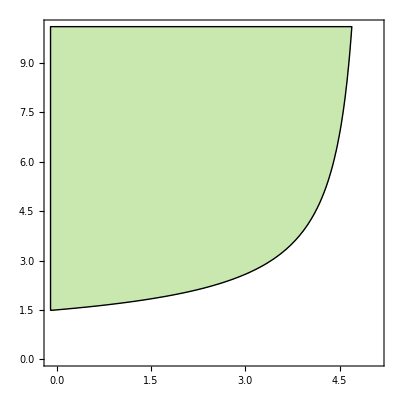
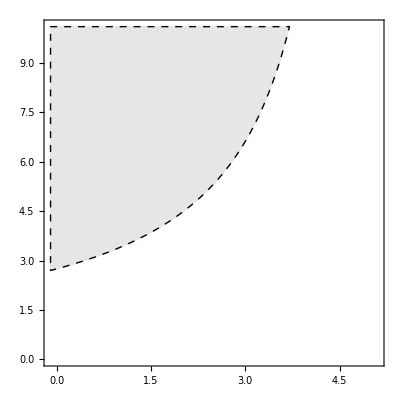
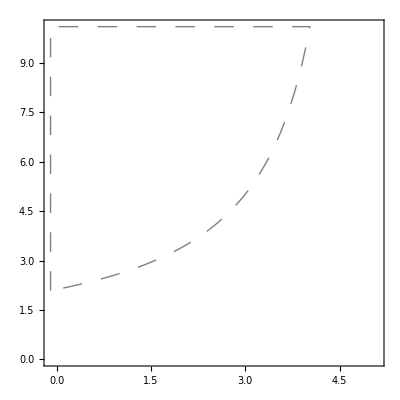
```mathematica
Persist=-Graphics-;Ant=-Graphics-;Ancestral=-Graphics-;

Needs["ErrorBarPlots`"]
Off[Greater::nord];
Off[Less::nord];
Off[Power::infy];
Off[Infinity::indet];
Off[General::obspkg];
Off[General::obspkg];
Off[ErrorBar::shdw];
Off[General::obspkg];
PS=Show[Persist,Ant,ErrorListPlot[{{{5-1,4.3},ErrorBar[0.4,0.6]}},PlotStyle->{Blue,Thickness[0.005],PointSize[0.03]}],ListPlot[{{5-1.2619089497454137,4.28908725309096}},PlotStyle->{Black,PointSize[0.04]}],ListPlot[{{5-3,9}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[White],Disk[]}],0.04}],Ancestral,FrameStyle->Black,PlotRange->{{0.1,4.9},{0.2,9.8}},FrameTicks->{Automatic,Automatic,None,None},AspectRatio->1,LabelStyle->Directive[FontSize->20]]
```

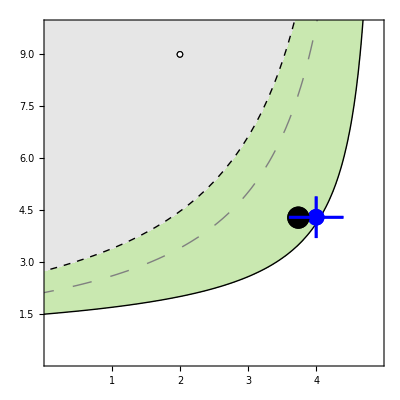

#### Plot ecological equilibria and evolutionary dynamics: Figure 3c,e

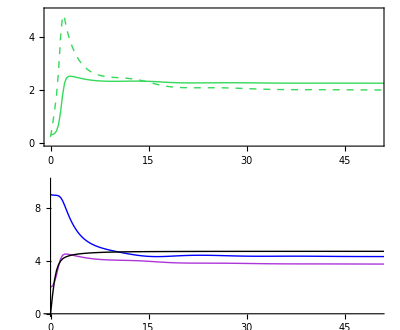

```mathematica
GraphicsGrid[{{Plot[{((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)/.eqsolEvo)[[1]],((Lw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)+(A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)/.eqsolEvo)[[1]]},{T,0,end},PlotStyle->{{RGBColor[54/255,217/255,89/255],Thick},{RGBColor[54/255,217/255,89/255],Dashed,Thick}},PlotRange->{{0,50},{0,5}},Frame->True,FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},AspectRatio->0.4,LabelStyle->Directive[FontSize->12]]},{Plot[{(vWmax/(1+Exp[-vSw((vPw[T]/.eqsolEvo)+(vIw[T]/.eqsolEvo))])/.evoParam)[[1]],5-(hWmax/(1+Exp[hSw ((hPw[T]/.eqsolEvo)-(hIw[T]/.eqsolEvo))])/.evoParam)[[1]],(bWmax(2/(1+Exp[-bSw (bPw[T]/.eqsolEvo)])-1)/.evoParam)[[1]]},{T,0,end},PlotRange->{{0,50},{0,10}},PlotStyle->{{Blue,Thick},{RGBColor[173/255,54/255,217/255],Thick},{Black,Thick}},TicksStyle->Black,AxesStyle->Black,AspectRatio->0.4,LabelStyle->Directive[FontSize->12]]}}]
```

#### D. discolor: Figure 3b

#### Parameter Space

NOTE: To simply create Figure 3b, please see section “Figure 3b” below.

```mathematica
(* Parameters: *)
param={hMax->5,H->0.1,ϵ->1,mW->0.005,mD->0.003,dW->0.25,dD->0.3,dA->0.2};

(* Population dynamics *)
dDwt=Dw'[t]==Dw[t]((1-Dw[t])+((bW vW A[t])/(H+vW A[t]))-hW Lw[t]);
dDdt=Dd'[t]==Dd[t]((1-Dd[t])+((bD vD A[t])/(H+vD A[t]))-hD Ld[t]);
dLwt=Lw'[t]==ϵ eW vW Dw[t] A[t]-mW hW Lw[t]-dW Lw[t];
dLdt=Ld'[t]==ϵ eD vD Dd[t] A[t]-mD hD Ld[t]-dD Ld[t];
dAt=A'[t]==mW hW Lw[t]+mD hD Ld[t]-dA A[t];
ecoEqsol=ParametricNDSolve[{dDwt/.param,dDdt/.param,dLwt/.param,dLdt/.param,dAt/.param,Dw[0]==1,Dd[0]==1,Lw[0]==0.1,Ld[0]==0.1,A[0]==0.1},{Dw,Dd,Lw,Ld,A},{t,0,end},{bW,vW,hW,bD,vD,hD,eW,eD}];

(* Parameter space *)
Off[ParametricNDSolve::ndsz]
Off[ParametricNDSolve::nrnum1]
Off[InterpolatingFunction::dmvali]
Off[NIntegrate::inumr]
Off[NIntegrate::sLdcon]
Off[NIntegrate::ncvb]
Off[Greater::nord]
Off[NIntegrate::slwcon]
Off[ParametricNDSolve::prange]
(* Ancestral M. sexta persists as pure herbivore *)
Ancestral=RegionPlot[{(A[0,9,3,0,vD,hD,0.9,0.7][end]>0.01)/.ecoEqsol/.hD->hMax-x/.param},{x,-0.1,5.1},{vD,-0.1,10.1},PlotStyle->Opacity[0],BoundaryStyle->{Gray,Dashing[Large],Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
(* M. sexta persists *)
Persist=RegionPlot[{(A[4.702452794067137,4.28908725309096,1.2619089497454137,3.5086384886875486,vD,hD,0.5946093045538515,0.6330065154140837][end]>0.0001)/.ecoEqsol/.hD->hMax-x/.param},{x,-0.1,5.1},{vD,0,10.1},PlotStyle->RGBColor[201/255,232/255,176/255],BoundaryStyle->{Black,Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
(* Net Antagonism *)
Ant=RegionPlot[{(Dd[4.702452794067137,4.28908725309096,1.2619089497454137,3.5086384886875486,vD,hD,0.5946093045538515,0.6330065154140837][end]<1&&A[4.702452794067137,4.28908725309096,1.2619089497454137,3.5086384886875486,vD,hD,0.5946093045538515,0.6330065154140837][end]>0.0001)/.ecoEqsol/.hD->hMax-x/.param},{x,-0.1,5.1},{vD,0,10.1},PlotStyle->GrayLevel[0.9],BoundaryStyle->{Black,Dashed,Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
```

#### Figure 3b

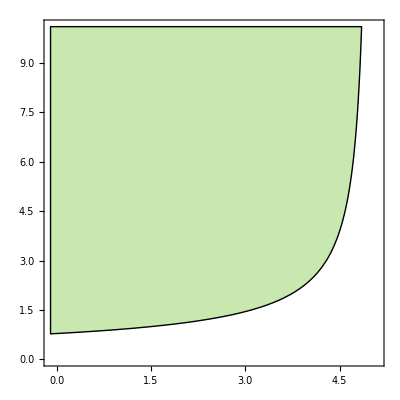
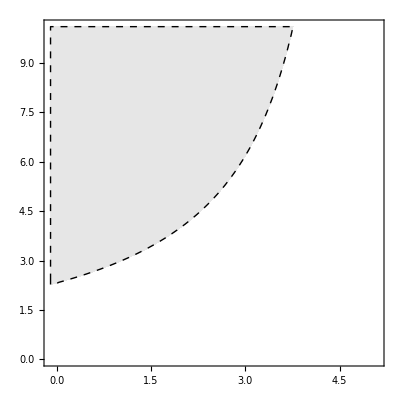
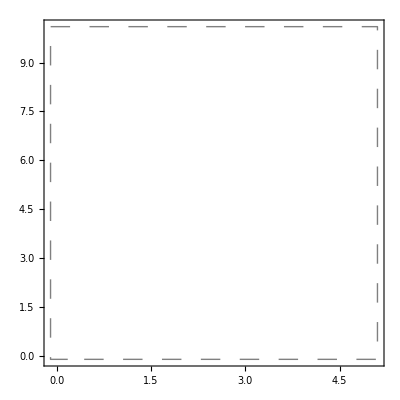
```mathematica
Persist=-Graphics-;Ant=-Graphics-;Ancestral=-Graphics-;

Needs["ErrorBarPlots`"]
Off[Greater::nord];
Off[Less::nord];
Off[Power::infy];
Off[Infinity::indet];
Off[General::obspkg];
Off[General::obspkg];
Off[ErrorBar::shdw];
Off[General::obspkg]
PS=Show[Persist,Ant,ErrorListPlot[{{{5-2,2.3},ErrorBar[0.8,0.4]}},PlotStyle->{Blue,Thickness[0.005],PointSize[0.03]}],ListPlot[{{5-2.460834691261736,2.2729162056617724}},PlotStyle->{Black,PointSize[0.04]}],ListPlot[{{5-1.5,9}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[White],Disk[]}],0.04}],Ancestral,FrameStyle->Black,PlotRange->{{0.1,4.9},{0.2,9.8}},FrameTicks->{Automatic,Automatic,None,None},AspectRatio->1,LabelStyle->Directive[FontSize->20]]
```

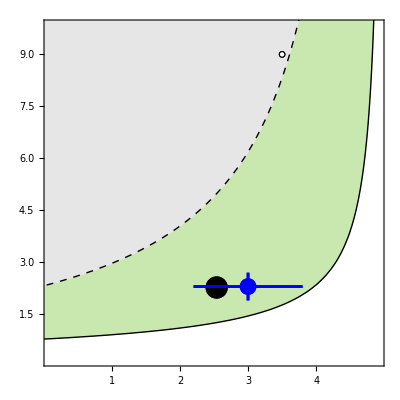

#### Plot ecological equilibria and evolutionary dynamics: Figure 3d,f

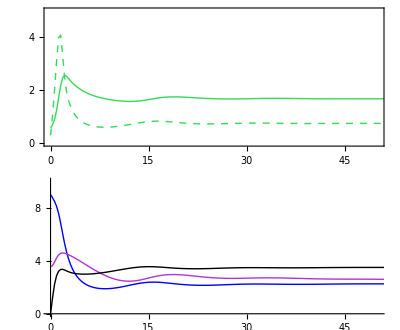

```mathematica
GraphicsGrid[{{Plot[{((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)/.eqsolEvo)[[1]],((Ld[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)+(A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)/.eqsolEvo)[[1]]},{T,0,end},PlotStyle->{{RGBColor[54/255,217/255,89/255],Thick},{RGBColor[54/255,217/255,89/255],Dashed,Thick}},PlotRange->{{0,50},{0,5}},Frame->True,FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},AspectRatio->0.4,LabelStyle->Directive[FontSize->12]]},{Plot[{(vDmax/(1+Exp[-vSd((vPd[T]/.eqsolEvo)+(vId[T]/.eqsolEvo))])/.evoParam)[[1]],5-(hDmax/(1+Exp[hSd ((hPd[T]/.eqsolEvo)-(hId[T]/.eqsolEvo))])/.evoParam)[[1]],(bDmax(2/(1+Exp[-bSd (bPd[T]/.eqsolEvo)])-1)/.evoParam)[[1]]},{T,0,end},PlotRange->{{0,50},{0,10}},PlotStyle->{{Blue,Thick},{RGBColor[173/255,54/255,217/255],Thick},{Black,Thick}},TicksStyle->Black,AxesStyle->Black,AspectRatio->0.4,LabelStyle->Directive[FontSize->12]]}}]
```

#### D. wrightii and P. parviflora: Figure 4a

#### Parameter Space

NOTE: To simply create Figure 4a, please see section “Figure 4a” below.

```mathematica
(* Parameters *)
param={hMax->5,H->0.1,ϵ->1,mW->0.005,mP->0.01,dW->0.25,dP->0.25,dA->0.2};

(* Population dynamics *)
dDwt=Dw'[t]==Dw[t]((1-Dw[t])+((bW vW A[t])/(H+vW A[t]))-hW Lw[t]);
dDpt=Dp'[t]==Dp[t]((1-Dp[t])-hP Lp[t]);
dLwt=Lw'[t]==ϵ eW vW Dw[t] A[t]-mW hW Lw[t]-dW Lw[t];
dLpt=Lp'[t]==ϵ eP vP Dp[t] A[t]-mP hP Lp[t]-dP Lp[t];
dAt=A'[t]==mW hW Lw[t]+mP hP Lp[t]-dA A[t];
ecoEqsol=ParametricNDSolve[{dDwt/.param,dDpt/.param,dLwt/.param,dLpt/.param,dAt/.param,Dw[0]==1,Dp[0]==1,Lw[0]==0.1,Lp[0]==0.1,A[0]==0.1},{Dw,Dp,Lw,Lp,A},{t,0,end},{bW,vW,hW,bP,vP,hP,eW,eP}];

(* Parameter space *)
Off[ParametricNDSolve::ndsz]
Off[ParametricNDSolve::nrnum1]
Off[InterpolatingFunction::dmvali]
Off[NIntegrate::inumr]
Off[NIntegrate::sLdcon]
Off[NIntegrate::ncvb]
Off[Greater::nord]
Off[NIntegrate::slwcon]
Off[ParametricNDSolve::prange]
(* Ancestral M. sexta persists as pure herbivore *)
Ancestral=RegionPlot[{(A[0,vW,hW,0,9,0.7,0.7,0.7][end]>0.01)/.ecoEqsol/.hW->hMax-x/.param},{x,-0.1,5.1},{vW,0,10.1},PlotStyle->Opacity[0],BoundaryStyle->{Gray,Dashing[Large],Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
(* M. sexta persists *)
Persist=RegionPlot[{(A[4.703177225069778,vW,hW,0,8.932249832317389,0.30289651489196123,0.6040532989283073,0.6021132703226388][end]>0.01)/.ecoEqsol/.hW->hMax-x/.param},{x,-0.1,5.1},{vW,0,10.1},PlotStyle->RGBColor[201/255,232/255,176/255],BoundaryStyle->{Black,Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
(* Net Antagonism *)
Ant=RegionPlot[{(Dw[4.703177225069778,vW,hW,0,8.932249832317389,0.30289651489196123,0.6040532989283073,0.6021132703226388][end]<1&&A[4.703177225069778,vW,hW,0,8.932249832317389,0.30289651489196123,0.6040532989283073,0.6021132703226388][end]>0.01)/.ecoEqsol/.hW->hMax-x/.param},{x,-0.1,5.1},{vW,0,10.1},PlotStyle->GrayLevel[0.9],BoundaryStyle->{Black,Dashed,Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
```

#### Figure 4a

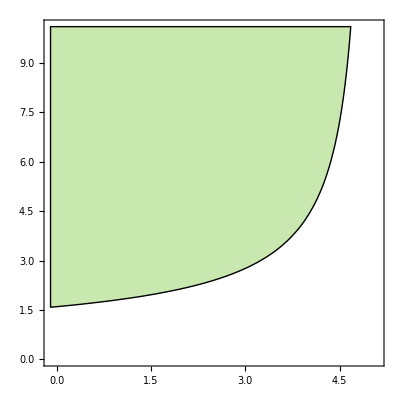
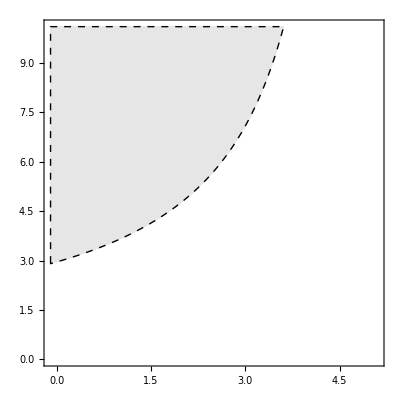
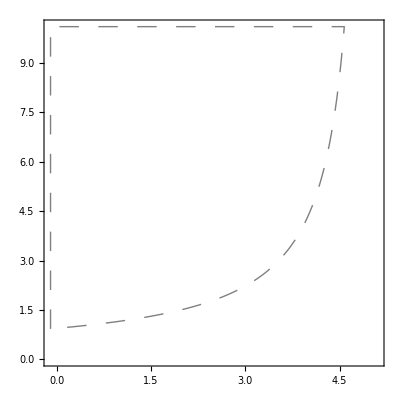
```mathematica
Persist=-Graphics-;Ant=-Graphics-;Ancestral=-Graphics-;

Needs["ErrorBabPlots`"]
Off[Greater::nord];
Off[Less::nord];
Off[Power::infy];
Off[Infinity::indet];
Off[General::obspkg];
Off[General::obspkg];
Off[ErrorBar::shdw];
Off[General::obspkg]
PS=Show[Persist,Ant,ListPlot[{{5-1.3,4.6}},PlotStyle->{Black,PointSize[0.04]}],ListPlot[{{5-1.4,9}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[White],Disk[]}],0.04}],Ancestral,FrameStyle->Black,PlotRange->{{0.1,4.9},{0.2,9.8}},FrameTicks->{Automatic,Automatic,None,None},AspectRatio->1,LabelStyle->Directive[FontSize->20]]
```

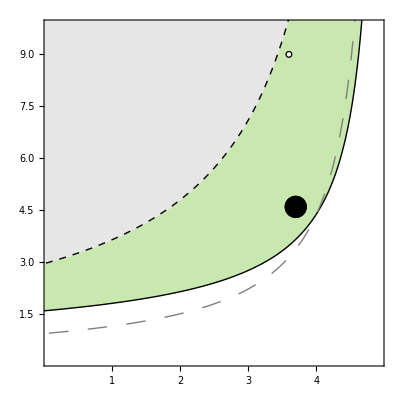

#### Plot ecological equilibria and evolutionary dynamics: Figure 4e,i

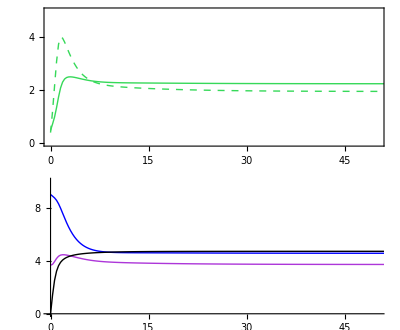

```mathematica
GraphicsGrid[{{Plot[{((Dw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)/.eqsolEvo)[[1]],((Lw[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)+(A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)/.eqsolEvo)[[1]]},{T,0,end},PlotStyle->{{RGBColor[54/255,217/255,89/255],Thick},{RGBColor[54/255,217/255,89/255],Dashed,Thick}},PlotRange->{{0,50},{0,5}},Frame->True,FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},AspectRatio->0.4,LabelStyle->Directive[FontSize->12]]},{Plot[{(vWmax/(1+Exp[-vSw((vPw[T]/.eqsolEvo)+(vIw[T]/.eqsolEvo))])/.evoParam)[[1]],5-(hWmax/(1+Exp[hSw ((hPw[T]/.eqsolEvo)-(hIw[T]/.eqsolEvo))])/.evoParam)[[1]],(bWmax(2/(1+Exp[-bSw (bPw[T]/.eqsolEvo)])-1)/.evoParam)[[1]]},{T,0,end},PlotRange->{{0,50},{0,10}},PlotStyle->{{Blue,Thick},{RGBColor[173/255,54/255,217/255],Thick},{Black,Thick}},TicksStyle->Black,AxesStyle->Black,AspectRatio->0.4,LabelStyle->Directive[FontSize->12]]}}]
```

#### D. discolor and P. parviflora: Figure 4b

#### Parameter Space

NOTE: To simply create Figure 4b, please see section “Figure 4b” below.

```mathematica
(* Parameters *)
param={hMax->5,H->0.1,ϵ->1,mD->0.003,mP->0.01,dD->0.3,dP->0.25,dA->0.2};

(* Population dynamics *)
dDdt=Dd'[t]==Dd[t]((1-Dd[t])+((bD vD A[t])/(H+vD A[t]))-hD Ld[t]);
dDpt=Dp'[t]==Dp[t]((1-Dp[t])-hP Lp[t]);
dLdt=Ld'[t]==ϵ eD vD Dd[t] A[t]-mD hD Ld[t]-dD Ld[t];
dLpt=Lp'[t]==ϵ eP vP Dp[t] A[t]-mP hP Lp[t]-dP Lp[t];
dAt=A'[t]==mD hD Ld[t]+mP hP Lp[t]-dA A[t];
ecoEqsol=ParametricNDSolve[{dDdt/.param,dDpt/.param,dLdt/.param,dLpt/.param,dAt/.param,Dd[0]==1,Dp[0]==1,Ld[0]==0.1,Lp[0]==0.1,A[0]==0.1},{Dd,Dp,Ld,Lp,A},{t,0,end},{bP,vP,hP,bD,vD,hD,eP,eD}];

(* Parameter space *)
Off[ParametricNDSolve::ndsz]
Off[ParametricNDSolve::nrnum1]
Off[InterpolatingFunction::dmvali]
Off[NIntegrate::inumr]
Off[NIntegrate::sLdcon]
Off[NIntegrate::ncvb]
Off[Greater::nord]
Off[NIntegrate::slwcon]
Off[ParametricNDSolve::prange]
(* Ancestral M. sexta persists as pure herbivore *)
Ancestral=RegionPlot[{(A[0,9,1,0,vD,hD,0.7,0.7][end]>0.02)/.ecoEqsol/.hD->hMax-x/.param},{x,-0.1,5.1},{vD,0,10.1},PlotStyle->Opacity[0],BoundaryStyle->{Gray,Dashing[Large],Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
(* M. sexta persists *)
Persist=RegionPlot[{(A[0,8.984127936876796,0.5615666783179312,3.6242261658103283,vD,hD,0.6329927322581461,0.7021912706325009][end]>0.02)/.ecoEqsol/.hD->hMax-x/.param},{x,-0.1,5.1},{vD,0,10.1},PlotStyle->RGBColor[201/255,232/255,176/255],BoundaryStyle->{Black,Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
(* Net Antagonism *)
NM=RegionPlot[{(Dd[0,8.984127936876796,0.5615666783179312,3.6242261658103283,vD,hD,0.6329927322581461,0.7021912706325009][end]<1&&A[0,8.984127936876796,0.5615666783179312,3.6242261658103283,vD,hD,0.6329927322581461,0.7021912706325009][end]>0.02)/.ecoEqsol/.hD->hMax-x/.param},{x,-0.1,5.1},{vD,0,10.1},PlotStyle->GrayLevel[0.9],BoundaryStyle->{Black,Dashed,Thick},FrameStyle->Black,AspectRatio->1,LabelStyle->Directive[FontSize->20]]
```

#### Figure 4b

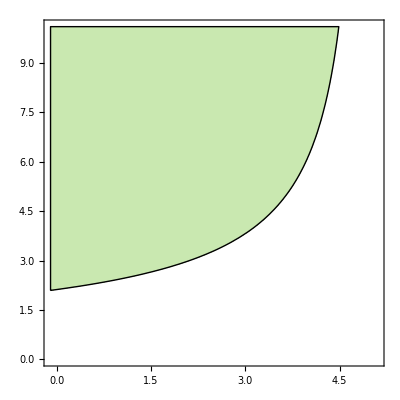
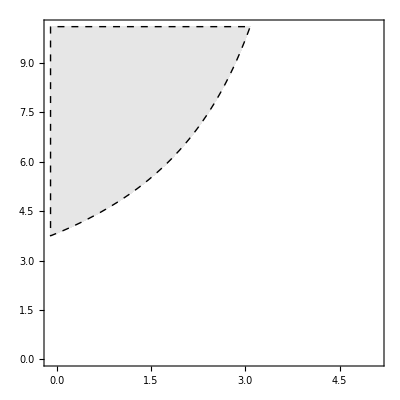
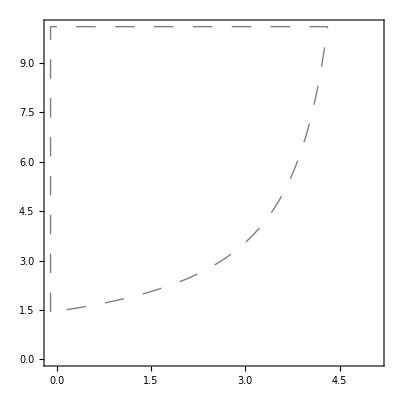
```mathematica
Persist=-Graphics-;Ant=-Graphics-;Ancestral=-Graphics-;

Needs["ErrorBabPlots`"]
Off[Greater::nord];
Off[Less::nord];
Off[Power::infy];
Off[Infinity::indet];
Off[General::obspkg];
Off[General::obspkg];
Off[ErrorBar::shdw];
Off[General::obspkg]
PS=Show[Persist,Ant,ListPlot[{{5-2.8860914356642358,3.9952543079087603}},PlotStyle->{Black,PointSize[0.04]}],ListPlot[{{5-1.3,9}},PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[White],Disk[]}],0.04}],Ancestral,FrameStyle->Black,PlotRange->{{0.1,4.9},{0.2,9.8}},FrameTicks->{Automatic,Automatic,None,None},AspectRatio->1,LabelStyle->Directive[FontSize->20]]
```

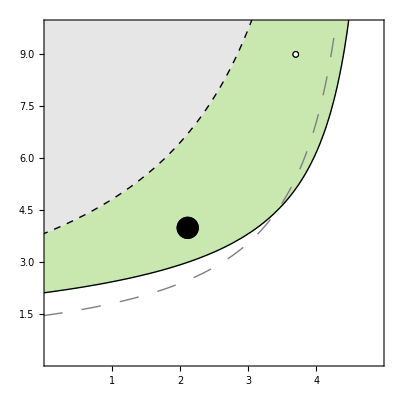

#### Plot ecological equilibria and evolutionary dynamics: Figure 4f,i

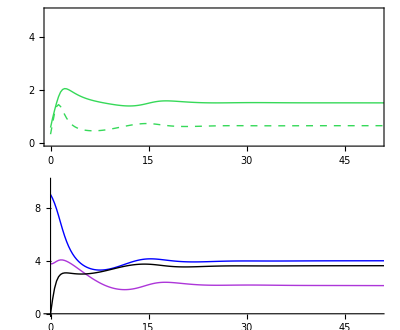

```mathematica
GraphicsGrid[{{Plot[{((Dd[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)/.eqsolEvo)[[1]],((Ld[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)+(A[hPw[T],vPw[T],bPw[T],hPd[T],vPd[T],bPd[T],hIw[T],vIw[T],hId[T],vId[T]][end]/.eqsol)/.eqsolEvo)[[1]]},{T,0,end},PlotStyle->{{RGBColor[54/255,217/255,89/255],Thick},{RGBColor[54/255,217/255,89/255],Dashed,Thick}},PlotRange->{{0,50},{0,5}},Frame->True,FrameStyle->{{Black,Opacity[0]},{Black,Opacity[0]}},AspectRatio->0.4,LabelStyle->Directive[FontSize->12]]},{Plot[{(vDmax/(1+Exp[-vSd((vPd[T]/.eqsolEvo)+(vId[T]/.eqsolEvo))])/.evoParam)[[1]],5-(hDmax/(1+Exp[hSd ((hPd[T]/.eqsolEvo)-(hId[T]/.eqsolEvo))])/.evoParam)[[1]],(bDmax(2/(1+Exp[-bSd (bPd[T]/.eqsolEvo)])-1)/.evoParam)[[1]]},{T,0,end},PlotRange->{{0,50},{0,10}},PlotStyle->{{Blue,Thick},{RGBColor[173/255,54/255,217/255],Thick},{Black,Thick}},TicksStyle->Black,AxesStyle->Black,AspectRatio->0.4,LabelStyle->Directive[FontSize->12]]}}]
```